## A366717: Smallest prime dividing 12^n - 1.

### MATHEMATICA PROGRAM:

```mathematica
Table[FactorInteger[12^n-1][[1,1]],{n,71}] (* Paul F.Marrero Romero, Oct 25 2023 *)
```

{11,11,11,5,11,7,11,5,11,11,11,5,11,11,11,5,11,7,11,5,11,11,11,5,11,11,11,5,11,7,11,5,11,11,11,5,11,11,11,5,11,7,11,5,11,11,11,5,11,11,11,5,11,7,11,5,11,11,11,5,11,11,11,5,11,7,11,5,11,11,11}

### Formula:

a(n) = A020639(A024140(n)).  - Paul F. Marrero Romero, Oct 25 2023

### Plot section:

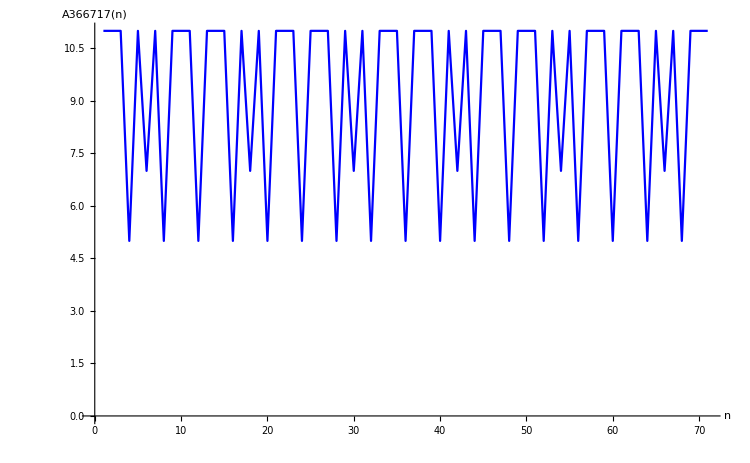

```mathematica
ListPlot[Table[FactorInteger[12^n-1][[1,1]],{n,71}], Joined->True, PlotStyle-> Blue, AxesLabel->{"n","A366717(n)"}, LabelStyle->Directive[Black,Bold]]
```

### References:

Sean A. Irvine, Smallest prime dividing 12^n - 1., Entry A366717 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366717